## IsoPerimetricRatio-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m;
```

Cellzilla2D (3.0.51d (10 June 2017)) loaded Sat 10 Jun 2017 18:48:17
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

## Compute isoperimetric ratio of a polygon specified by the coordinates of its vertices

```mathematica
polygon={{0.6656821861024209,0.5885139068629628},{0.3674265409089722,0.548792012192189},{-0.5083022778120968,0.03200749861905844},{-0.9625187848327785,-0.40634552703524995},{-0.603944818863048,-0.6296344493677282},{-0.2938861906733466,-0.19134629851828722},{0.3771323695082593,0.14124017268253336}};
```

```mathematica
IsoPerimetricRatio[polygon]
```

0.403407

## Calculate the same ratio using the formula 4 π A /P from geometry

```mathematica
4*Pi*areafunction[polygon]/perimeterLength[polygon]^2
```

0.403407

## Calculate the isoperimetric ratios of all the cells in a tissue and plot the histogram of the vaues

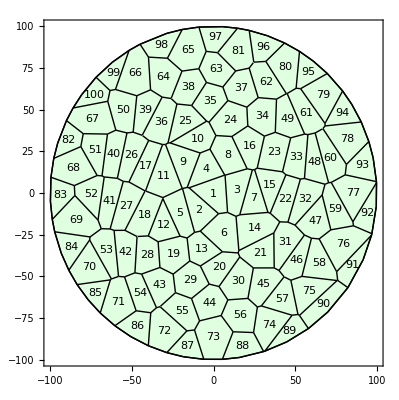

```mathematica
w=TemplateRandomCircularGrid[100,100];
ShowTissue[w,"CellNumbers"->True, Frame-> True]
```

```mathematica
IsoPerimetricRatio[w,1] (* single cell *)
```

0.675176

```mathematica
IPR=IsoPerimetricRatio[w]
```

{0.675176,0.65042,0.677369,0.680511,0.66394,0.811883,0.567329,0.791278,0.653317,0.701822,0.675881,0.650649,0.819621,0.756495,0.63432,0.78732,0.603563,0.719321,0.868256,0.767757,0.739397,0.660462,0.797873,0.876283,0.669616,0.653147,0.655913,0.801261,0.890931,0.803924,0.714684,0.652779,0.711174,0.862703,0.842031,0.741596,0.867654,0.843032,0.684004,0.652404,0.611238,0.703384,0.81484,0.882997,0.7948,0.651648,0.746215,0.58185,0.717772,0.793404,0.683315,0.689274,0.654232,0.725147,0.805514,0.886861,0.703859,0.694665,0.652956,0.612569,0.687118,0.775416,0.867955,0.827757,0.862793,0.781415,0.805578,0.820268,0.799284,0.724569,0.811469,0.81194,0.872355,0.718775,0.634602,0.734079,0.696736,0.760532,0.745566,0.775095,0.835325,0.68153,0.662549,0.643087,0.623081,0.718101,0.679284,0.722054,0.514562,0.557148,0.448978,0.515854,0.688931,0.639355,0.656588,0.706287,0.697086,0.650284,0.569682,0.656192}

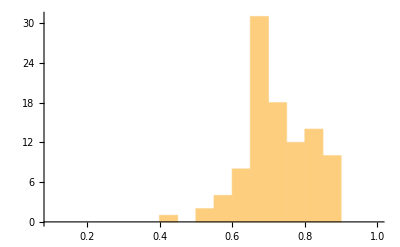

```mathematica
Histogram[IPR, {.1,1,.05}]
```